Authors:Eldhose Benny

Department of Physics, National Institute of Technology Calicut, Kozhikode, Kerala 673601, India
                                Email: eldhosebenny771@gmail.com/eldhose_b200147ep@nitc.ac.in

Dr. Sreenath K. Manikandan

Researcher in Theoretical Physics                 
                                Nordita, Stockholm University and KTH Royal Institute of Technology,
                                Hannes Alfv.b4ens v¨ag 12, SE-106 91 Stockholm, Sweden
                                Email: sreenath.k.manikandan@su.se

```mathematica
omega=.;k=.;gamma=.;n=.;dt=.;
```

Here omega is Ω(energy of excited state), k is γ_w(spontaneous emission rate), gamma is γ_m(spin measurement rate),  and n is ⟨n⟩(average occupation of the environment)

```mathematica
H0=omega{{1,0},{0,0}};
```

```mathematica
sx={{0,1},{1,0}};
rho={{r11,r12},{r21,r22}};
rhs={{r11,rx-I ry},{rx+I ry,1-r11}};
Ad={{0,1},{0,0}};Aa={{0,0},{1,0}};
```

Tilted Lindblad Generator:

```mathematica
TLnG=dt(-I (H0.rho-rho.H0)+(n+1)k (Exp[-se]Aa.rho.Ad-1/2(Ad.Aa.rho+rho.Ad.Aa))+n k (Exp[-sa] Ad.rho.Aa -1/2(Aa.Ad.rho+rho.Aa.Ad)))-gamma (sx.(sx.rho-rho.sx)-(sx.rho-rho.sx).sx)dt
```

{{-dt gamma (2 r11-2 r22)+dt (-k (1+n) r11+ⅇ^-sa k n r22),dt (-1/2 k n r12-1/2 k (1+n) r12-ⅈ omega r12)-dt gamma (2 r12-2 r21)},{-dt gamma (-2 r12+2 r21)+dt (-1/2 k n r21-1/2 k (1+n) r21+ⅈ omega r21),-dt gamma (-2 r11+2 r22)+dt (ⅇ^-se k (1+n) r11-k n r22)}}

## Numerical Simulations

### Solution for steady state (when se=0 & sa =0 ):

```mathematica
Solve[dt(-I (H0.rhs-rhs.H0)+(n+1)k (Aa.rhs.Ad-1/2(Ad.Aa.rhs+rhs.Ad.Aa))+n k ( Ad.rhs.Aa -1/2(Aa.Ad.rhs+rhs.Aa.Ad)))-gamma (sx.(sx.rhs-rhs.sx)-(sx.rhs-rhs.sx).sx)dt=={{0,0},{0,0}},{r11,rx,ry}]
```

{{r11→-(-2 gamma-k n)/(4 gamma+k+2 k n),rx→0,ry→0}}

### Simulation over 8 x10^4 trajectories, using 2000 time step and time increment of dt=0.0005

```mathematica
omega=1;k=4; n=1;dt=0.0005;rho=.;
```

```mathematica
NumSim=ParallelTable[{gamma,cta={};cte={};cto={};Do[counta=0;counte=0;counto=0;For[m=0,m<2000+1,m++,rho[0]={{-(-2 gamma-k n)/(4 gamma+k+2 k n),0},{0,1+(-2 gamma-k n)/(4 gamma+k+2 k n)}};
M0={{0,Sqrt[n k dt]},{0,0}};
M1={{Sqrt[1-(n+1)k dt],0},{0,Sqrt[1-n k dt]}};
M2={{0,0},{Sqrt[(n+1)k dt],0}};M[m]=RandomChoice[{Chop[Tr[M0.(rho[m]-dt I (H0.rho[m]-rho[m].H0)-gamma (sx.(sx.rho[m]-rho[m].sx)-(sx.rho[m]-rho[m].sx).sx)dt).Transpose[M0]]],Chop[Tr[M1.(rho[m]-dt I (H0.rho[m]-rho[m].H0)-gamma (sx.(sx.rho[m]-rho[m].sx)-(sx.rho[m]-rho[m].sx).sx)dt).Transpose[M1]]],Chop[Tr[M2.(rho[m]-dt I (H0.rho[m]-rho[m].H0)-gamma (sx.(sx.rho[m]-rho[m].sx)-(sx.rho[m]-rho[m].sx).sx)dt).Transpose[M2]]]}->{M0,M1,M2},1][[1]];
If[M[m]==M0 ,counta+=1,counta+=0];If[M[m]==M2 ,counte+=1,counte+=0];If[M[m]==M2 || M[m]==M0,counto+=1,counto+=0];
rho[m+1]=M[m].(rho[m]-dt I (H0.rho[m]-rho[m].H0)-gamma (sx.(sx.rho[m]-rho[m].sx)-(sx.rho[m]-rho[m].sx).sx)dt).Transpose[M[m]]/Tr[M[m].(rho[m]-dt I (H0.rho[m]-rho[m].H0)-gamma (sx.(sx.rho[m]-rho[m].sx)-(sx.rho[m]-rho[m].sx).sx)dt).Transpose[M[m]]];
];AppendTo[cta,counta];AppendTo[cte,counte];AppendTo[cto,counto];,{80000}];Mean[cta],Variance[cta],Mean[cte],Variance[cte],Mean[cto],Variance[cto]},{gamma,{0.1,2.1,2.83,4.1,6.1,8.1,10.1}}]
```

{{0.1,211531/80000,10344316039/6399920000,8673/3200,16592575/10239872,107089/20000,2347226079/399995000},{2.1,191121/80000,11845803359/6399920000,51543/16000,572519151/255996800,112209/20000,2252720319/399995000},{2.83,186789/80000,12087069479/6399920000,132571/40000,3846129959/1599980000,451931/80000,36080211239/6399920000},{4.1,182249/80000,12316101999/6399920000,34339/10000,263555579/99998750,456961/80000,36229124479/6399920000},{6.1,177033/80000,12472836911/6399920000,142827/40000,4605288071/1599980000,462687/80000,36453620031/6399920000},{8.1,43601/20000,783292799/399995000,291607/80000,19589437551/6399920000,466011/80000,36510627879/6399920000},{10.1,85787/40000,3156910631/1599980000,148103/40000,5120141391/1599980000,23389/4000,91718679/15999800}}

```mathematica
NumSim={{0.1,211531/80000,10344316039/6399920000,8673/3200,16592575/10239872,107089/20000,2347226079/399995000},{2.1,191121/80000,11845803359/6399920000,51543/16000,572519151/255996800,112209/20000,2252720319/399995000},{2.83,186789/80000,12087069479/6399920000,132571/40000,3846129959/1599980000,451931/80000,36080211239/6399920000},{4.1,182249/80000,12316101999/6399920000,34339/10000,263555579/99998750,456961/80000,36229124479/6399920000},{6.1,177033/80000,12472836911/6399920000,142827/40000,4605288071/1599980000,462687/80000,36453620031/6399920000},{8.1,43601/20000,783292799/399995000,291607/80000,19589437551/6399920000,466011/80000,36510627879/6399920000},{10.1,85787/40000,3156910631/1599980000,148103/40000,5120141391/1599980000,23389/4000,91718679/15999800}}
```

{{0.1,211531/80000,10344316039/6399920000,8673/3200,16592575/10239872,107089/20000,2347226079/399995000},{2.1,191121/80000,11845803359/6399920000,51543/16000,572519151/255996800,112209/20000,2252720319/399995000},{2.83,186789/80000,12087069479/6399920000,132571/40000,3846129959/1599980000,451931/80000,36080211239/6399920000},{4.1,182249/80000,12316101999/6399920000,34339/10000,263555579/99998750,456961/80000,36229124479/6399920000},{6.1,177033/80000,12472836911/6399920000,142827/40000,4605288071/1599980000,462687/80000,36453620031/6399920000},{8.1,43601/20000,783292799/399995000,291607/80000,19589437551/6399920000,466011/80000,36510627879/6399920000},{10.1,85787/40000,3156910631/1599980000,148103/40000,5120141391/1599980000,23389/4000,91718679/15999800}}

Here the each of the column represents the following:  1 → γ_m, 2→Mean of absorption event, 3→Variance of absorption event, 4→Mean of emission event, 5→Variance of emission event , 6→Mean of null event, 7→Variance of null event

## Large Deviation Approach

```mathematica
k=.;n=.;gamma=.;dt=.;
```

### Eigenvalues of tilted Lindblad generator

```mathematica
Eqs={-dt gamma (2 r11-2 r22)+dt (-k (1+n) r11+ⅇ^-sa k n r22),dt (-1/2 k n r12-1/2 k (1+n) r12-ⅈ omega r12)-dt gamma (2 r12-2 r21),-dt gamma (-2 r12+2 r21)+dt (-1/2 k n r21-1/2 k (1+n) r21+ⅈ omega r21),-dt gamma (-2 r11+2 r22)+dt (ⅇ^-se k (1+n) r11-k n r22)}
```

{-dt gamma (2 r11-2 r22)+dt (-k (1+n) r11+ⅇ^-sa k n r22),dt (-ⅈ r12-(k n r12)/2-1/2 k (1+n) r12)-dt gamma (2 r12-2 r21),-dt gamma (-2 r12+2 r21)+dt (ⅈ r21-(k n r21)/2-1/2 k (1+n) r21),-dt gamma (-2 r11+2 r22)+dt (ⅇ^-se k (1+n) r11-k n r22)}

```mathematica
ldss=Normal@CoefficientArrays[Eqs,{r11,r12,r21,r22}][[2]]/dt//Simplify
```

{{-2 gamma-k (1+n),0,0,2 gamma+ⅇ^-sa k n},{0,-ⅈ-2 gamma-1/2 k (1+2 n),2 gamma,0},{0,2 gamma,ⅈ-2 gamma-1/2 k (1+2 n),0},{ⅇ^-se (2 ⅇ^se gamma+k+k n),0,0,-2 gamma-k n}}

```mathematica
Eigenvalues[ldss]//FullSimplify
```

{-2 gamma-ⅇ^(-sa-se) √(ⅇ^(2 (sa+se)) (-1+4 gamma^2))-1/2 k (1+2 n),-2 gamma+ⅇ^(-sa-se) √(ⅇ^(2 (sa+se)) (-1+4 gamma^2))-1/2 k (1+2 n),-2 gamma-1/2 k (1+2 n)-1/2 ⅇ^(-sa-se) √(ⅇ^(sa+se) (4 k (1+n) (2 ⅇ^sa gamma+k n)+ⅇ^se (ⅇ^sa (16 gamma^2+k^2)+8 gamma k n))),1/2 ⅇ^(-sa-se) (-ⅇ^(sa+se) (4 gamma+k+2 k n)+√(ⅇ^(sa+se) (4 k (1+n) (2 ⅇ^sa gamma+k n)+ⅇ^se (ⅇ^sa (16 gamma^2+k^2)+8 gamma k n))))}

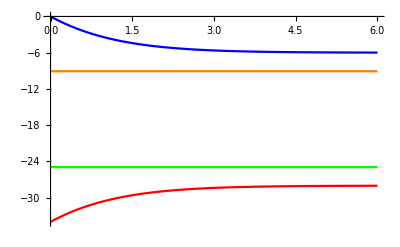

```mathematica
k=6;gamma=4;omega=1;sa=0;n=1;
Plot[{-2 gamma-1/2 k (1+2 n)-1/2 ⅇ^(-sa-se) √(ⅇ^(sa+se) (4 k (1+n) (2 ⅇ^sa gamma+k n)+ⅇ^se (ⅇ^sa (16 gamma^2+k^2)+8 gamma k n))),1/2 ⅇ^(-sa-se) (-ⅇ^(sa+se) (4 gamma+k+2 k n)+√(ⅇ^(sa+se) (4 k (1+n) (2 ⅇ^sa gamma+k n)+ⅇ^se (ⅇ^sa (16 gamma^2+k^2)+8 gamma k n)))),-2 gamma-1/2 k (1+2 n)-ⅇ^(-sa-se) √(ⅇ^(2 (sa+se)) (4 gamma^2-omega^2)),-2 gamma-1/2 k (1+2 n)+ⅇ^(-sa-se) √(ⅇ^(2 (sa+se)) (4 gamma^2-omega^2))},{se,0,6},PlotStyle->{Red,Blue,Green,Orange}]
```

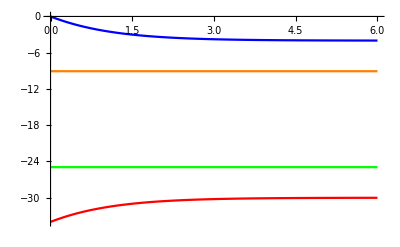

```mathematica
k=6;gamma=4;omega=1;se=0;n=1;
Plot[{-2 gamma-1/2 k (1+2 n)-1/2 ⅇ^(-sa-se) √(ⅇ^(sa+se) (4 k (1+n) (2 ⅇ^sa gamma+k n)+ⅇ^se (ⅇ^sa (16 gamma^2+k^2)+8 gamma k n))),1/2 ⅇ^(-sa-se) (-ⅇ^(sa+se) (4 gamma+k+2 k n)+√(ⅇ^(sa+se) (4 k (1+n) (2 ⅇ^sa gamma+k n)+ⅇ^se (ⅇ^sa (16 gamma^2+k^2)+8 gamma k n)))),-2 gamma-1/2 k (1+2 n)-ⅇ^(-sa-se) √(ⅇ^(2 (sa+se)) (4 gamma^2-omega^2)),-2 gamma-1/2 k (1+2 n)+ⅇ^(-sa-se) √(ⅇ^(2 (sa+se)) (4 gamma^2-omega^2))},{sa,0,6},PlotStyle->{Red,Blue,Green,Orange}]
```

```mathematica
k=.;gamma=.;se=.;sa=.;n=.;
LD=1/2 ⅇ^(-sa-se) (-ⅇ^(sa+se) (4 gamma+k+2 k n)+√(ⅇ^(sa+se) (4 k (1+n) (2 ⅇ^sa gamma+k n)+ⅇ^se (ⅇ^sa (16 gamma^2+k^2)+8 gamma k n))))
```

1/2 ⅇ^(-sa-se) (-ⅇ^(sa+se) (4 gamma+k+2 k n)+√(ⅇ^(sa+se) (4 k (1+n) (2 ⅇ^sa gamma+k n)+ⅇ^se (ⅇ^sa (16 gamma^2+k^2)+8 gamma k n))))

LD  is the largest eigenvalue of  the tilted Lindblad generator (LD is the moment generating function).

### Absorption events

#### Average

```mathematica
AvAb=-D[LD,sa]/.sa->0/.se->
0//FullSimplify
```

(k n (2 gamma+k+k n))/(√((4 gamma+k+2 k n)^2))

#### Variance

```mathematica
VarAb=D[LD,{sa,2}]/.sa->0/.se->0//FullSimplify
```

(k n (2 gamma+k+k n) ((4 gamma+k)^2+2 k (6 gamma+k) n+2 k^2 n^2))/(((4 gamma+k+2 k n)^2)^(3/2))

#### Mandel’s Q parameter

```mathematica
QAb=VarAb/AvAb-1//FullSimplify
```

-(2 k n (2 gamma+k+k n))/(4 gamma+k+2 k n)^2

#### Plotting and comparison with Numerical simulation

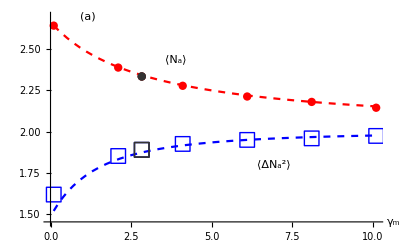

```mathematica
k=4;n=1;dt=0.0005;PlotAb=Show[Plot[((k n (2 gamma+k+k n))/(√((4 gamma+k+2 k n)^2)))2000dt,{gamma,0.1,10.1},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black]},Epilog->{{Style[Text["⟨N_a⟩",Scaled[{0.39,0.78}]],16,Red]},{Style[Text["⟨ΔN_a^2⟩",Scaled[{0.68,0.29}]],16,Blue]},{Style[Text["(a)",Scaled[{0.13,0.98}]],16,Black]}},PlotRange->{1.45,2.7}],Plot[ ((k n (2 gamma+k+k n) ((4 gamma+k)^2+2 k (6 gamma+k) n+2 k^2 n^2))/(((4 gamma+k+2 k n)^2)^(3/2)))2000dt,{gamma,0.1,10.1},PlotStyle->{Dashed,Blue}],ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[2]]},{i,1,Length[NumSim]}],PlotStyle->{Red,PointSize[0.015]}],
ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[2]]}},PlotStyle->{GrayLevel[0.2],PointSize[0.015]}],ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[3]]},{i,1,Length[NumSim]}],PlotMarkers->{"□",15},PlotStyle->{Blue}],ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[3]]}},PlotMarkers->{"□",15},PlotStyle->{GrayLevel[0.2]}]]
```

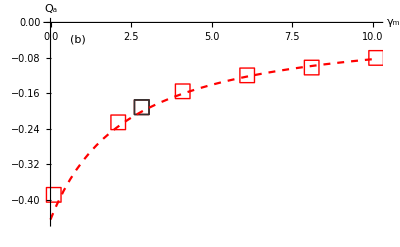

```mathematica
PlotQAb=Show[ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[3]]/NumSim[[i]][[2]]-1},{i,1,Length[NumSim]}], PlotMarkers->{"□",15},PlotStyle->{Red},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black],Style["Q_a",Italic,24,Black]},Epilog->{Style[Text["(b)",Scaled[{0.1,0.9}]],16,Black]},PlotRange->{-0.45,0}],ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[3]]/NumSim[[3]][[2]]-1}},PlotMarkers->{"□",15},PlotStyle->{GrayLevel[0.2]}],Plot[-(2 k n(2 gamma+k+k n))/(4 gamma+k+2 k n)^2,{gamma,0,10},PlotStyle->{Dashed,Red}]]
```

### Emission events

```mathematica
k=.;n=.;
```

#### Average

```mathematica
AvEm=-D[LD,se]/.se->0/.sa->
0//FullSimplify
```

(k (1+n) (2 gamma+k n))/(√((4 gamma+k+2 k n)^2))

#### Variance

```mathematica
VarEm=D[LD,{se,2}]/.se->0/.sa->0//FullSimplify
```

(k (1+n) (2 gamma+k n) (16 gamma^2+4 gamma (k+3 k n)+k^2 (1+2 n (1+n))))/(((4 gamma+k+2 k n)^2)^(3/2))

#### Mandel’s Q parameter

```mathematica
QEm=VarEm/AvEm-1//FullSimplify
```

-(2 k (1+n) (2 gamma+k n))/(4 gamma+k+2 k n)^2

#### Plotting and comparison with Numerical simulation

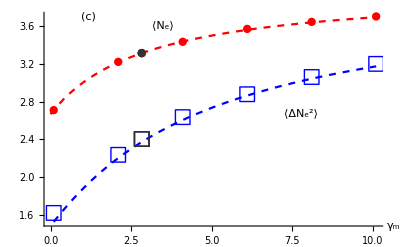

```mathematica
k=4;n=1;dt=0.0005;PlotEm=Show[Plot[((k (1+n) (2 gamma+k n))/(√((4 gamma+k+2 k n)^2)))2000dt,{gamma,0,10},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black]},Epilog->{{Style[Text["⟨N_e⟩",Scaled[{0.35,0.94}]],16,Red]},{Style[Text["⟨ΔN_e^2⟩",Scaled[{0.76,0.53}]],16,Blue]},{Style[Text["(c)",Scaled[{0.13,0.98}]],16,Black]}},PlotRange->All],Plot[ ((k (1+n) (2 gamma+k n) (16 gamma^2+4 gamma (k+3 k n)+k^2 (1+2 n (1+n))))/(((4 gamma+k+2 k n)^2)^(3/2)))2000dt,{gamma,0.1,10.1},PlotStyle->{Dashed,Blue}],ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[4]]},{i,1,Length[NumSim]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[4]]}},PlotStyle->{GrayLevel[0.2],PointSize[0.015]}],ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[5]]},{i,1,Length[NumSim]}],PlotMarkers->{"□",15},PlotStyle->{Blue}],ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[5]]}},PlotMarkers->{"□",15},PlotStyle->{GrayLevel[0.2]}]]
```

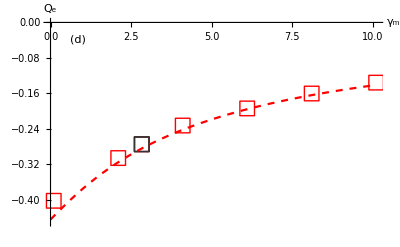

```mathematica
PlotQEm=Show[ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[5]]/NumSim[[i]][[4]]-1},{i,1,Length[NumSim]}], PlotMarkers->{"□",15},PlotStyle->{Red},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black],Style["Q_e",Italic,24,Black]},Epilog->{Style[Text["(d)",Scaled[{0.1,0.9}]],16,Black]},PlotRange->{-0.45,0}],ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[5]]/NumSim[[3]][[4]]-1}},PlotMarkers->{"□",15},PlotStyle->{GrayLevel[0.2]}],Plot[-(2 k (1+n) (2 gamma+k n))/(4 gamma+k+2 k n)^2,{gamma,0,10},PlotStyle->{Dashed,Red}]]
```

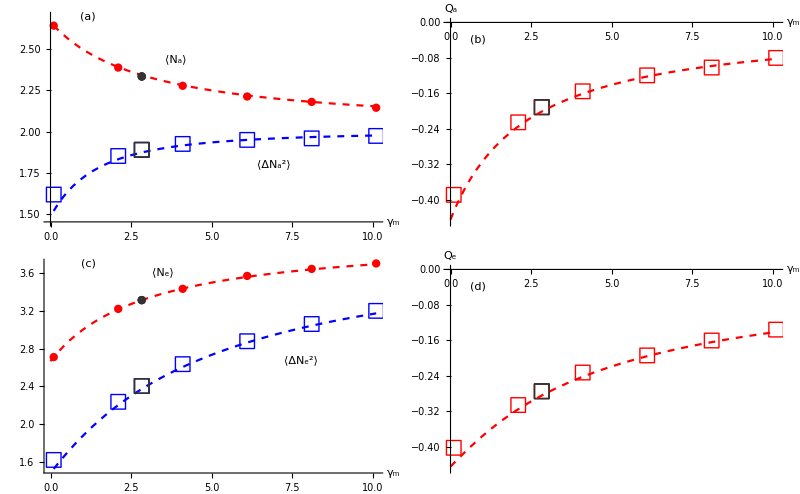

```mathematica
GraphicsGrid[{{PlotAb,PlotQAb},{PlotEm,PlotQEm}},Spacings->{0, 0},ImageSize->800]
```

### Negation of null events

```mathematica
k=.;n=.;
```

#### Average

```mathematica
AvNu={-D[LD,sa]+-D[LD,se]}/.se->0/.sa->0//FullSimplify
```

{(2 k (gamma+2 gamma n+k n (1+n)))/(√((4 gamma+k+2 k n)^2))}

Avg OverTilde[null] = Avg absorption + Avg emission

#### Variance

```mathematica
VarNu={D[LD,{sa,2}]+D[LD,{se,2}]+2D[LD,sa,se]}/.sa->0/.se->0//FullSimplify
```

{(2 k (16 gamma^3 (1+2 n)+2 k^3 n (1+n) (1+2 n (1+n))+4 gamma^2 k (1+12 n (1+n))+gamma k^2 (1+2 n) (1+12 n (1+n))))/(((4 gamma+k+2 k n)^2)^(3/2))}

Var OverTilde[null]= Var absorption + Var emission + 2*Covariance

Covariance=D[LD,sa,se]/.sa→0/.se→0=(k^2 n (1+n) (8 gamma^2+4 gamma (k+2 k n)+k^2 (1+2 n (1+n))))/(((4 gamma+k+2 k n)^2)^(3/2))

#### Mandel’s Q parameter

```mathematica
QNu=VarNu/AvNu-1//FullSimplify
```

{(-4 gamma^2 k+k^3 n (1+n))/((4 gamma+k+2 k n)^2 (gamma+2 gamma n+k n (1+n)))}

#### Plotting and comparison with Numerical simulation

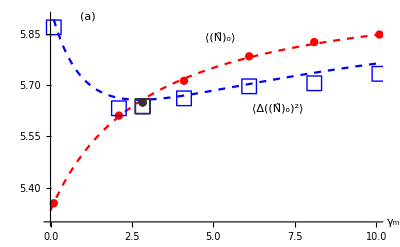

```mathematica
k=4;n=1;dt=0.0005;PlotNu=Show[Plot[((2 k (gamma+2 gamma n+k n (1+n)))/(√((4 gamma+k+2 k n)^2)))2000dt,{gamma,0,10},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black]},Epilog->{{Style[Text["⟨(Ñ)_o⟩",Scaled[{0.52,0.88}]],16,Red]},{Style[Text["⟨Δ((Ñ)_o)^2⟩",Scaled[{0.69,0.55}]],16,Blue]},{Style[Text["(a)",Scaled[{0.13,0.98}]],16,Black]}},PlotRange->{5.3,5.9}],Plot[ ((2 k (16 gamma^3 (1+2 n)+2 k^3 n (1+n) (1+2 n (1+n))+4 gamma^2 k (1+12 n (1+n))+gamma k^2 (1+2 n) (1+12 n (1+n))))/(((4 gamma+k+2 k n)^2)^(3/2)))2000dt,{gamma,0.1,10.1},PlotStyle->{Dashed,Blue}],ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[6]]},{i,1,Length[NumSim]}],PlotStyle->{Red,PointSize[0.015]}],
ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[6]]}},PlotStyle->{GrayLevel[0.2],PointSize[0.015]}],ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[7]]},{i,1,Length[NumSim]}],PlotMarkers->{"□",15},PlotStyle->{Blue}],ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[7]]}},PlotMarkers->{"□",15},PlotStyle->{GrayLevel[0.2]}]]
```

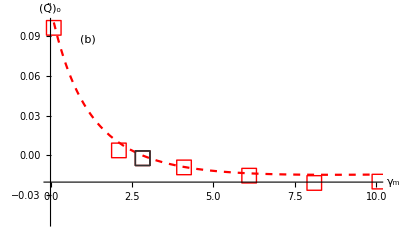

```mathematica
PlotQNu=Show[Plot[(-4 gamma^2 k+k^3 n (1+n))/((4 gamma+k+2 k n)^2 (gamma+2 gamma n+k n (1+n))),{gamma,0,10},PlotStyle->{Dashed,Red},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black],Style["(Q̃)_o",Italic,24,Black]},Epilog->{Style[Text["(b)",Scaled[{0.13,0.9}]],16,Black]},AxesOrigin->{0,-0.02},PlotRange->{-0.05,0.1}],ListPlot[Table[{NumSim[[i]][[1]],NumSim[[i]][[7]]/NumSim[[i]][[6]]-1},{i,1,Length[NumSim]}], PlotMarkers->{"□",15},PlotStyle->{Red}],ListPlot[{{NumSim[[3]][[1]],NumSim[[3]][[7]]/NumSim[[3]][[6]]-1}},PlotMarkers->{"□",15},PlotStyle->{GrayLevel[0.2]}]]
```

#### Transition Point(Q=0)

```mathematica
k=.;n=.;
Solve[(-4 gamma^2 k+k^3 n (1+n))/((4 gamma+k+2 k n)^2 (gamma+2 gamma n+k n (1+n)))==0,gamma]
```

{{gamma→-1/2 k √(n+n^2)},{gamma→1/2 k √(n+n^2)}}

At  γ_m=  (γ_w √(⟨n⟩^2+⟨n⟩))/2  we get a transition from super-Poissonian to sub-Poissonian photon statistics. When γ_w=4 & average occupation ⟨n⟩ =1, the transition point occurs at  γ_m= 2.83

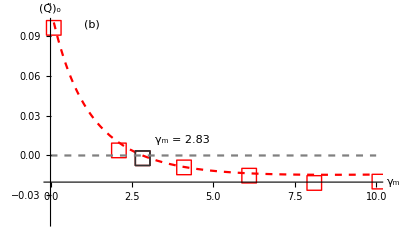

```mathematica
PlotQNu=Show[PlotQNu,Plot[0.00,{gamma,0,10},PlotStyle->{Dashed,Gray}],Epilog->{{Style[Text["(b)",Scaled[{0.14,0.97}]],16,Black]},{Style[Text["γ_m = 2.83",Scaled[{0.41,0.415}]],14,GrayLevel[0.2]]}}]
```

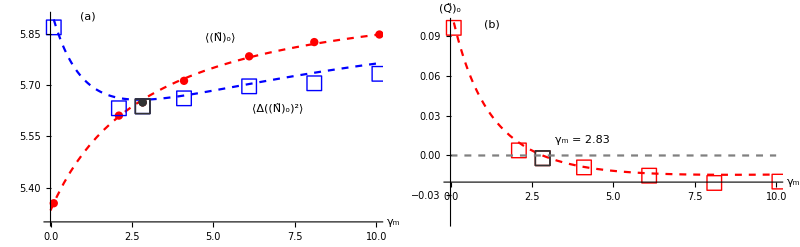

```mathematica
GraphicsGrid[{{PlotNu,PlotQNu}},Spacings->{0, 0},ImageSize->800]
```

Note: The plots in the appendix are generated using the same code for ⟨n⟩=0.5, with its transition point occurring at γ_m=1.73